```mathematica
deltav = Sqrt[2 g R (Sin[θ]/(1+Sin[θ]))]
tof = 2*Sqrt[R/g] * (( (1+Sin[θ])/2)^(3/2) * ArcCos[Cos[θ]/(1+Sin[θ])] + 1/2 Cos[θ] Sqrt[Sin[θ]])
```

√2 √((g R Sin[θ])/(1+Sin[θ]))

2 √(R/g) (1/2 Cos[θ] √Sin[θ]+(ArcCos[Cos[θ]/(1+Sin[θ])] (1+Sin[θ])^(3/2))/(2 √2))

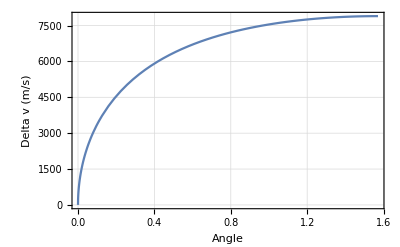

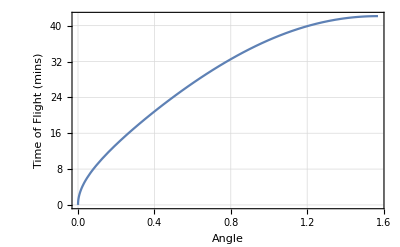

```mathematica
Plot[deltav/.{R-> 6350000, g-> 9.81},{θ,0,π/2},GridLines->Automatic,Frame-> True, FrameLabel->{"Angle","Delta v (m/s)"}]
Plot[tof/60/.{R-> 6350000, g-> 9.81},{θ,0,π/2},GridLines->Automatic,Frame-> True, FrameLabel->{"Angle","Time of Flight (mins)"}]
```

```mathematica
1000/60//N
```

16.6667

```mathematica
MR = Exp[deltav/c]
```

ⅇ^((√2 √((g R Sin[θ])/(1+Sin[θ])))/c)

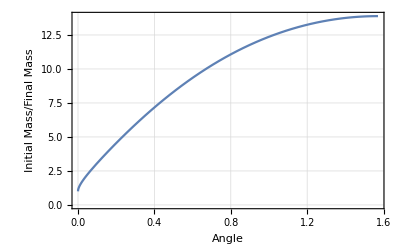

```mathematica
Plot[MR/.{R-> 6350000, g-> 9.81,c-> 3000},{θ,0,π/2},GridLines->Automatic,Frame-> True, FrameLabel->{"Angle","Initial Mass/Final Mass"}]
```

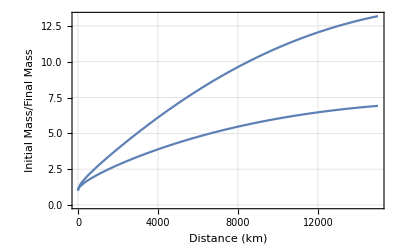

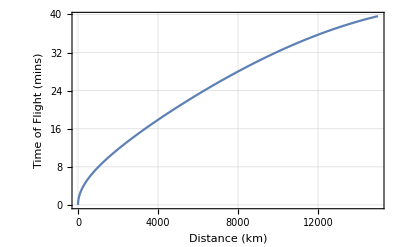

```mathematica
Plot[(MR/.{θ -> 1000S/(2R)})/.{R-> 6350000, g-> 9.81,c->{3000,4000}},{S,0,15000},GridLines->Automatic,Frame-> True, FrameLabel->{"Distance (km)","Initial Mass/Final Mass"}]
Plot[(tof/60/.{θ -> 1000S/(2R)})/.{R-> 6350000, g-> 9.81},{S,0,15000},GridLines->Automatic,Frame-> True, FrameLabel->{"Distance (km)","Time of Flight (mins)"}]
```

```mathematica
/.{
```

ⅇ^((√2 √((g R Sin[S/(2 R)])/(1+Sin[S/(2 R)])))/c)

```mathematica
ClearAll[θ]
```

```mathematica
θ -> S/(2R)
```

θ→S/(2 R)

```mathematica
tof/.{θ -> S/(2R)}//FullSimplify
```

```mathematica
tof2=1/2 √(R/g) (√2 ArcSec[Sec[S/(2 R)]+Tan[S/(2 R)]] (1+Sin[S/(2 R)])^(3/2)+Sin[S/R]/(√Sin[S/(2 R)]))
```

1/2 √(R/g) (√2 ArcSec[Sec[S/(2 R)]+Tan[S/(2 R)]] (1+Sin[S/(2 R)])^(3/2)+Sin[S/R]/(√Sin[S/(2 R)]))

```mathematica
tofAirplane = S/vairplane/.vairplane-> 300
```

S/300

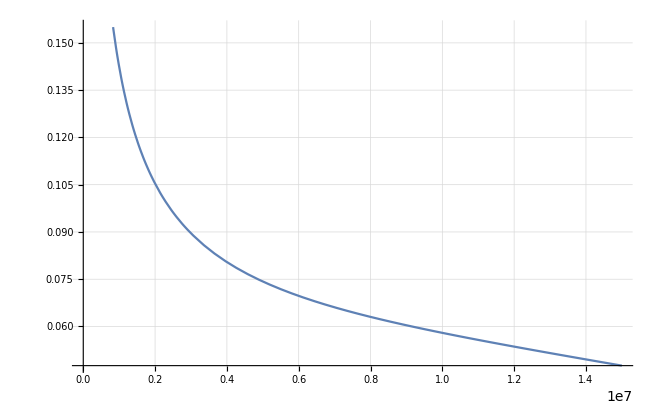

```mathematica
Plot[tof2/tofAirplane/.{R-> 6350000, g-> 9.81},{S,0,15000000},GridLines->Automatic]
```

```mathematica
NSolve[tof2/tofAirplane/.{R-> 6350000, g-> 9.81}==0.1,S]
```

ReplaceAll::reps: {{R→6350000,g→9.81}==0.1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {(R→6350000)==0.1&&(g→9.81)==0.1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NSolve[(150 √(R/g) (√2 ArcSec[Sec[S/(2 R)]+Tan[S/(2 R)]] (1+Sin[S/(2 R)])^(3/2)+Sin[S/R]/(√Sin[S/(2 R)])))/S/.{R→6350000,g→9.81}==0.1,S]

```mathematica
tof2/tofAirplane/.{R-> 6350000, g-> 9.81}
```

```mathematica
FindRoot[1/S 120682.31098005307 (√2 ArcSec[Sec[S/12700000]+Tan[S/12700000]] (1+Sin[S/12700000])^(3/2)+Sin[S/6350000]/(√Sin[S/12700000]))==0.05,{S,5000000}]
```

{S→1.37757×10^7}